# Relativistic Quantum Mechanics

## TISE: The Barrier Potential

```mathematica
Subscript[V, 0] :=2
a := 2
ℏ :=1
m :=1
```

```mathematica
f[x_]:=Piecewise[{{0,x<0},{Subscript[V,0],0<=x<=2}}];
Plot[f[x],{x,-4,4},PlotStyle->Thick,AxesLabel->{"x","f(x)"},Filling->Axis]
```

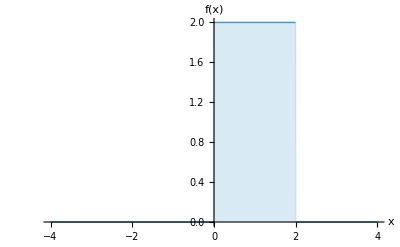

The time-independent Schrodinger Equation has different forms in the regions to the left and right of the barrier potential:

First region x<0:

```mathematica
sol1 = DSolve[-ℏ^2/(2 m) Subscript[ψ, 1]''[x] == En Subscript[ψ, 1][x],Subscript[ψ, 1][x],x];
TrigToExp[sol1]
```

{{ψ_1[x]→1/2 ⅇ^(-ⅈ √2 √En x) C[1]+1/2 ⅇ^(ⅈ √2 √En x) C[1]+1/2 ⅈ ⅇ^(-ⅈ √2 √En x) C[2]-1/2 ⅈ ⅇ^(ⅈ √2 √En x) C[2]}}

Let k1 =  (√(2 m En))/ℏ^2

```mathematica
Subscript[ψ, 1][x_] :=A Exp[I k1 x] +B Exp[-I k1 x]
```

Second Region 0<x>a

```mathematica
sol2= DSolve[-ℏ^2/(2 m) Subscript[ψ, 2]''[x]+V0 Subscript[ψ, 2][x] == En Subscript[ψ, 2][x],Subscript[ψ, 2][x],x];
TrigToExp[sol2]
```

{{ψ_2[x]→ⅇ^(√2 √(2-En) x) C[1]+ⅇ^(-√2 √(2-En) x) C[2]}}

Let k2 =  (√(2 m (En-V0)))/ℏ^2

√2 √(-2+En)

```mathematica
Subscript[ψ, 2][x_]:=C Exp[I k2 x]+ D Exp[-I k2 x]
```

Third Region x>a

```mathematica
sol3=DSolve[-ℏ^2/(2 m) Subscript[ψ, 3]''[x] == En Subscript[ψ, 3][x],Subscript[ψ, 3][x],x];
TrigToExp[sol3]
```

{{ψ_3[x]→1/2 ⅇ^(-ⅈ √2 √En x) C[1]+1/2 ⅇ^(ⅈ √2 √En x) C[1]+1/2 ⅈ ⅇ^(-ⅈ √2 √En x) C[2]-1/2 ⅈ ⅇ^(ⅈ √2 √En x) C[2]}}

```mathematica
Subscript[ψ, 3][x_]:=F Exp[I k1 x]+G Exp[-I k1 x]/.{G->0}
```

We apply the matching conditions for ψ(x) and ψ’(x), that is at the points x=0 and x=a, four equations in the arbitrary constants A, B, C, D, and F will be obtained:

```mathematica
eq1 = Subscript[ψ, 1][0]==Subscript[ψ, 2][0]
```

A+B==C+D

```mathematica
eq2 = Subscript[ψ, 2][a] == Subscript[ψ, 3][a]
```

D ⅇ^(-2 ⅈ k2)+C ⅇ^(2 ⅈ k2)==ⅇ^(2 ⅈ k1) F

```mathematica
eq3 = Subscript[ψ, 1]'[0] == Subscript[ψ, 2]'[0]
```

ⅈ A k1-ⅈ B k1==ⅈ C k2-ⅈ D k2

```mathematica
eq4 = eq2 = Subscript[ψ, 2]'[a] == Subscript[ψ, 3]'[a]
```

-ⅈ D ⅇ^(-2 ⅈ k2) k2+ⅈ C ⅇ^(2 ⅈ k2) k2==ⅈ ⅇ^(2 ⅈ k1) F k1

Solve this systems of equations:

```mathematica
Solve[{eq1,eq2,eq3,eq4},{B,C,D,F}]
```

{{B→-(A (-1+ⅇ^(4 ⅈ k2)) (-k1^2+k2^2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2),C→-(2 A k1 (k1+k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2),D→(2 A ⅇ^(4 ⅈ k2) k1 (k1-k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2),F→-(4 A ⅇ^(-2 ⅈ k1+2 ⅈ k2) k1 k2)/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2)}}

Thus we have:

```mathematica
B=-(A (-1+ⅇ^(4 ⅈ k2)) (-k1^2+k2^2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);
C1=-(2 A k1 (k1+k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);D1=(2 A ⅇ^(4 ⅈ k2) k1 (k1-k2))/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);F=-(4 A ⅇ^(-2 ⅈ k1+2 ⅈ k2) k1 k2)/(-k1^2+ⅇ^(4 ⅈ k2) k1^2-2 k1 k2-2 ⅇ^(4 ⅈ k2) k1 k2-k2^2+ⅇ^(4 ⅈ k2) k2^2);
```

Thus we have:

```mathematica
Subscript[ψ, I][x_] :=A Exp[I k1 x] +B Exp[-I k1 x];
Subscript[ψ, II][x_]:=C Exp[I k2 x]+ D Exp[-I k2 x];
Subscript[ψ, III][x_]:=F Exp[I k1 x]+G Exp[-I k1 x]/.{G->0};
```

with:

```mathematica
k1 =  (√(2 m En))/ℏ^2 ;
k2 =  (√(2 m (En-V0)))/ℏ^2 ;
```

The Reflection coefficient  R of the barrier is:

```mathematica
R= Abs[B/A]^2
```

Abs[((-1+ⅇ^(4 ⅈ √2 √(En-V0))) (-2 En+2 (En-V0)))/(-2 En+2 ⅇ^(4 ⅈ √2 √(En-V0)) En-4 √En √(En-V0)-4 ⅇ^(4 ⅈ √2 √(En-V0)) √En √(En-V0)-2 (En-V0)+2 ⅇ^(4 ⅈ √2 √(En-V0)) (En-V0))]^2

```mathematica
Rf[En_,V0_]:=Abs[((-1+ⅇ^(4 ⅈ √2 √(En-V0))) (-2 En+2 (En-V0)))/(-2 En+2 ⅇ^(4 ⅈ √2 √(En-V0)) En-4 √En √(En-V0)-4 ⅇ^(4 ⅈ √2 √(En-V0)) √En √(En-V0)-2 (En-V0)+2 ⅇ^(4 ⅈ √2 √(En-V0)) (En-V0))]^2
```

And the transmission coefficient T of the barrier is:

```mathematica
T = Abs[F/A]
```

8 ⅇ^(2 √2 Im[√En]-2 √2 Im[√(En-V0)]) Abs[(√En √(En-V0))/(-2 En+2 ⅇ^(4 ⅈ √2 √(En-V0)) En-4 √En √(En-V0)-4 ⅇ^(4 ⅈ √2 √(En-V0)) √En √(En-V0)-2 (En-V0)+2 ⅇ^(4 ⅈ √2 √(En-V0)) (En-V0))]

```mathematica
Tf[En_,V0_]:=8 ⅇ^(2 √2 Im[√En]-2 √2 Im[√(En-V0)]) Abs[(√En √(En-V0))/(-2 En+2 ⅇ^(4 ⅈ √2 √(En-V0)) En-4 √En √(En-V0)-4 ⅇ^(4 ⅈ √2 √(En-V0)) √En √(En-V0)-2 (En-V0)+2 ⅇ^(4 ⅈ √2 √(En-V0)) (En-V0))]
```

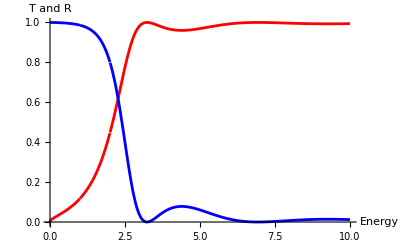

```mathematica
V0=2;
Plot[{Tf[En,2],Rf[En,2]},{En,0,10},PlotStyle->{Red,Blue}, AxesLabel->{"Energy","T and R"}]
```

Now we fix the energy to E=1.1 and we vary values over the potential V_0:

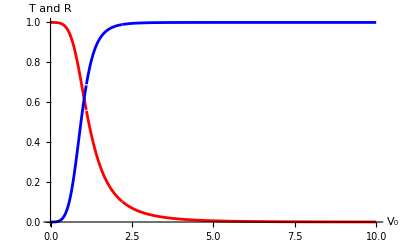

```mathematica
En=1.1;
Plot[{Tf[En,V],Rf[En,V]},{V,0,10},PlotStyle->{Red,Blue},AxesLabel->{"V_0","T and R"}]
```